```mathematica
ClearAll["Global`*"]
```

#### Equation (11) from Dors and Kletzing [1999]

Tm in eV
dens_m in cm^-3
pot in eV
RB the mirror ratio

```mathematica
speedOfLight=299792458;
inMass=5.1099891*^5/speedOfLight^2;
eCharge=1.602*^-19;
```

```mathematica
jDors[kappa_,Tm_,densm_,pot_,RB_]:= eCharge (1*^6 densm )√((Tm(1-3/(2 kappa)))/(2 π inMass))kappa/(kappa-1)Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])RB(1-(1-1/RB)(1+(pot/Tm)/((kappa-3/2)(RB-1)))^(1-kappa));
jDorsPotBar[kappa_,Tm_,densm_,potBar_,RB_]:= eCharge (1*^6 densm )√((Tm(1-3/(2 kappa)))/(2 π inMass))kappa/(kappa-1)Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])RB(1-(1-1/RB)(1+potBar/((kappa-3/2)(RB-1)))^(1-kappa));
```

## Analytic expression for evolution of kappa plasma density passing through potential drop ΔΦ, à la Liemohn and Khazanov [1998] method

```mathematica
phiBarK[phiBar_,κ_]:=phiBar/(1-3/(2 κ));
```

```mathematica
densFacK[phiBarK_,RB_,κ_]:=1/4( 2 (phiBarK-κ)^(1/2-κ) κ^(-1/2+κ) Csc[π κ]+1/(phiBarK^(3/2) √π √κ)(Gamma[κ]/((-1+RB) Gamma[5/2+κ]) ((-1+RB) κ ((-1+RB)^2 κ^2+phiBarK (-1+RB) κ (5+2 κ)+phiBarK^2 (1-2 κ (3+2 κ)))-(phiBarK+(-1+RB) κ)^3 Hypergeometric2F1[1,1+κ,-1/2,phiBarK/(κ-RB κ)])+(4 phiBarK^2 π Csc[π κ] Hypergeometric2F1Regularized[-1/2,1,1-κ,κ/phiBarK])/Gamma[-1/2+κ]));
```

Input data for computation of reduced chi-squared

```mathematica
medianPotAbove=941;
pAbove=medianPotAbove;
TFAST=110; (*eV*)
nFAST = 1.88;(*cm^-3*)
```

```mathematica
TandNString=ToString[StringForm["TFAST_eq_`1`-nFAST_eq_`2`",NumberForm[TFAST,{4,1},NumberPoint->"_"],NumberForm[nFAST,3,NumberPoint->"_"]]];
```

```mathematica
mapKappaList={1505/1000,1510/1000,1515/1000,1520/1000,1525/1000,1530/1000,1535/1000,1540/1000,1545/1000,1550/1000,1555/1000,1560/1000,1565/1000,1570/1000,1575/1000,1580/1000,1585/1000,1590/1000,1595/1000,1600/1000,1605/1000,1610/1000,1615/1000,1620/1000,1625/1000,1630/1000,1635/1000,1640/1000,1645/1000,1650/1000,1655/1000,1660/1000,1665/1000,1670/1000,1675/1000,1680/1000,1685/1000,1690/1000,1695/1000,1700/1000,1705/1000,1710/1000,1715/1000,1720/1000,1725/1000,1730/1000,1735/1000,1740/1000,1745/1000,1750/1000,1755/1000,1760/1000,1765/1000,1770/1000,1775/1000,1780/1000,1785/1000,1790/1000,1795/1000,1800/1000,1805/1000,1810/1000,1815/1000,1820/1000,1825/1000,1830/1000,1835/1000,1840/1000,1845/1000,1850/1000,1855/1000,1860/1000,1865/1000,1870/1000,1875/1000,1880/1000,1885/1000,1890/1000,1895/1000,1900/1000,1905/1000,1910/1000,1915/1000,1920/1000,1925/1000,1930/1000,1935/1000,1940/1000,1945/1000,1950/1000,1955/1000,1960/1000,1965/1000,1970/1000,1975/1000,1980/1000,1985/1000,1990/1000,1995/1000,2010/1000,2050/1000,2100/1000,2200/1000,2300/1000,2400/1000,2500/1000,2600/1000,2700/1000,2800/1000,2900/1000,3010/1000,3250/1000,3500/1000,3750/1000,4010/1000,4250/1000,4500/1000,4750/1000,5010/1000,5250/1000,5500/1000,5750/1000,6010/1000,6250/1000,6500/1000,6750/1000,7010/1000,7250/1000,7500/1000,7750/1000,8010/1000};
(*mapRBList =Flatten[{PowerRange[5,1*^4,1.05],10000.00}];*)
mapRBList={1.2432627,1.3054258,1.3706971,1.4392319,1.5111935,1.5867532,1.6660909,1.7493954,1.8368652,1.9287084,2.0251439,2.1264011,2.2327211,2.3443572,2.4615750,2.5846538,2.7138865,2.8495808,2.9920598,3.1416628,3.2987460,3.4636833,3.6368674,3.8187108,4.0096463,4.2101287,4.4206351,4.6416669,4.8737502,5.1174377,5.3733096,5.6419751,5.9240738,6.2202775,6.5312914,6.8578560,7.2007488,7.5607862,7.9388255,8.3357668,8.7525551,9.1901829,9.6496920,10.132177,10.638785,11.170725,11.729261,12.315724,12.931510,13.578086,14.256990,14.969840,15.718331,16.504248,17.329460,18.195933,19.105730,20.061017,21.064067,22.117271,23.223134,24.384291,25.603506,26.883681,28.227865,29.639258,31.121221,32.677282,34.311146,36.026704,37.828039,39.719441,41.705413,43.790683,45.980218,48.279229,50.693190,53.227849,55.889242,58.683704,61.617889,64.698784,67.933723,71.330409,74.896929,78.641776,82.573865,86.702558,91.037686,95.589570,100.36905,105.38750,110.65688,116.18972,121.99921,128.09917,134.50412,141.22933,148.29080,155.70534,163.49060,171.66513,180.24839,189.26081,198.72385,208.66004,219.09305,230.04770,241.55008,253.62759,266.30897,279.62441,293.60564,308.28592,323.70021,339.88522,356.87949,374.72346,393.45963,413.13261,433.78924,455.47871,478.25264,502.16527,527.27354,553.63721,581.31908,610.38503,640.90428,672.94949,706.59697,741.92682,779.02316,817.97432,858.87303,901.81668,946.90752,994.25289,1043.9655,1096.1638,1150.9720,1208.5206,1268.9466,1332.3940,1399.0137,1468.9644,1542.4126,1619.5332,1700.5099,1785.5354,1874.8121,1968.5527,2066.9804,2170.3294,2278.8458,2392.7881,2486.5253};
lenRB=Length[mapRBList];
lenKappa=Length[mapKappaList];
StringForm["N elem to compute: `1` (`2`, `3`)",lenKappa*lenRB,lenKappa,lenRB]
```

N elem to compute: 20567 (131, 157)

#### Open ze file

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/";
(*fil=FileNameJoin[{dir,"kappaBarbosaFacs.txt"}]*)
```

```mathematica
(*outStream=OpenWrite[fil]*)
```

```mathematica
(*Close[outStream];*)
```

```mathematica
(*FilePrint[fil]*)
```

#### Just to see if we can print

```mathematica
listKRun=lenKappa;listRRun=lenRB;
```

```mathematica
listKRun=2;listRRun=4;
```

```mathematica
For[iK=1,iK≤listKRun,iK++,tmpFile=FileNameJoin[{dir,ToString[StringForm["kappaLandKFacs_`1`_of_`2`.txt",iK,listKRun]]}];Print[tmpFile];outStream=OpenWrite[tmpFile];For[iR=1,iR≤listRRun,iR++,WriteString[outStream,StringForm["`1`,`2`,`3`,`4`,`5`,`6`\n",(iK-1)*lenRB+iR,iK,iR,NumberForm[mapKappaList[[iK]],{4,3}],NumberForm[mapRBList[[iR]],{4,1}],"BRO"]]];Close[outStream]]
```

```mathematica
For[iK=1,iK≤listKRun,iK++,tmpFile=FileNameJoin[{dir,ToString[StringForm["kappaLandKFacs_`1`_of_`2`.txt",iK,listKRun]]}];Print[tmpFile];Print["\n"];FilePrint[tmpFile]]
```

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs_1_of_2.txt

General::noopen: Cannot open /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs_1_of_2.txt.

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs_2_of_2.txt

General::noopen: Cannot open /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs_2_of_2.txt.

#### Now the real thing

```mathematica
listKRun=lenKappa;listRRun=lenRB;
```

```mathematica
listKRun=lenKappa;listRRun=lenRB;
```

```mathematica
For[iK=1,iK≤listKRun,iK++,tmpFile=FileNameJoin[{dir,ToString[StringForm["kappaLandKFacs-`1`--`2`_of_`3`.txt",TandNString,iK,listKRun]]}];Print[tmpFile];
Unprotect[outStream];Clear[outStream];
outStream=OpenWrite[tmpFile];For[iR=1,iR≤listRRun,iR++,WriteString[outStream,StringForm["`1`,`2`,`3`,`4`,`5`,`6`\n",(iK-1)*lenRB+iR,iK,iR,NumberForm[N[mapKappaList[[iK]]],{4,3}],NumberForm[mapRBList[[iR]],{5,3}],NumberForm[densFacK[phiBarK[pAbove/TFAST,mapKappaList[[iK]]],mapRBList[[iR]],mapKappaList[[iK]]],6]]]];Close[outStream]]
```

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--1_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--2_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--3_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--4_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--5_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--6_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--7_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--8_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--9_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--10_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--11_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--12_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--13_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--14_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--15_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--16_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--17_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--18_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--19_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--20_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--21_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--22_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--23_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--24_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--25_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--26_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--27_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--28_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--29_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--30_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--31_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--32_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--33_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--34_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--35_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--36_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--37_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--38_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--39_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--40_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--41_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--42_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--43_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--44_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--45_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--46_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--47_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--48_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--49_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--50_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--51_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--52_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--53_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--54_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--55_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--56_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--57_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--58_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--59_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--60_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--61_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--62_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--63_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--64_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--65_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--66_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--67_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--68_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--69_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--70_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--71_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--72_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--73_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--74_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--75_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--76_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--77_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--78_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--79_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--80_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--81_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--82_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--83_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--84_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--85_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--86_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--87_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--88_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--89_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--90_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--91_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--92_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--93_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--94_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--95_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--96_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--97_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--98_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--99_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--100_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--101_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--102_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--103_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--104_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--105_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--106_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--107_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--108_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--109_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--110_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--111_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--112_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--113_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--114_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--115_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--116_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--117_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--118_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--119_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--120_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--121_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--122_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--123_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--124_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--125_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--126_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--127_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--128_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--129_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--130_of_131.txt

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--131_of_131.txt

```mathematica
For[iK=1,iK≤listKRun,iK++,tmpFile=FileNameJoin[{dir,ToString[StringForm["kappaLandKFacs-`1`--`2`_of_`3`.txt",TandNString,iK,listKRun]]}];Print[tmpFile];FilePrint[tmpFile]]
```

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--1_of_2.txt

1,1,1,1.505,5.0,0.059673
2,1,2,1.505,5.2,0.0626631
3,1,3,1.505,5.5,0.0658018
4,1,4,1.505,5.8,0.0690966
158,2,1,1.510,5.0,0.0836036
159,2,2,1.510,5.2,0.0877913
160,2,3,1.510,5.5,0.0921861
161,2,4,1.510,5.8,0.0967982

/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/kappaLandKFacs-TFAST_eq_110_0-nFAST_eq_1_88--2_of_2.txt

## Plot Figure 2 in Dors and Kletzing [1999]

```mathematica
kappaList={1000,10,5,3,2,1.6};
RBList={3,10,30,100,1000};
```

```mathematica
grayLev1=0.4;
grayLev2=0.6;
tick=0.002;
kappaStyles={Directive[Dashing[{0,0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{0,Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Small}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Large,Large}],GrayLevel[grayLev2],Thickness[tick]],Directive[Dashing[{Small}],GrayLevel[grayLev1],Thickness[tick]],Directive[GrayLevel[grayLev2],Thickness[tick]]};
```

```mathematica
T=110;
n=1;
```

```mathematica
jDors[10,T,n,1000,5]
```

1.25371×10^-6

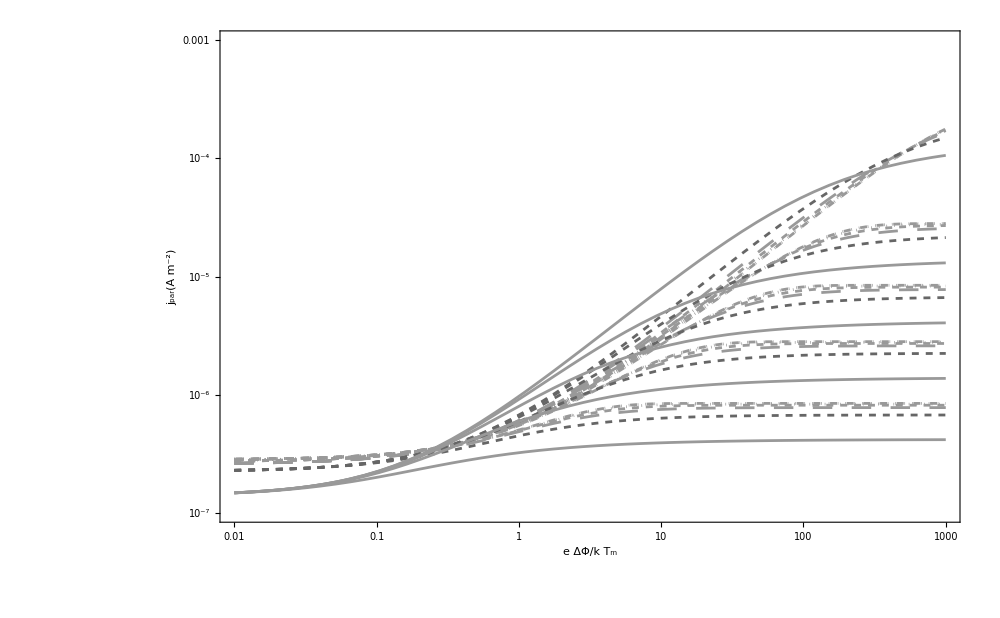

```mathematica
Show[Table[LogLogPlot[jDorsPotBar[kappaList[[j]],T,n,potBar,RBList[[k]]],{potBar,0.01,1000},PlotRange->{{0.01,1000},{1*^-7,1*^-3}},Frame->True,ImageSize->1000,FrameLabel->{StringForm["e ΔΦ/k T_m"],StringForm["j_par(A m^-2)"]},LabelStyle->(FontSize->18),PlotStyle->kappaStyles[[j]] ],{j,1,6},{k,1,5}]]
```